```mathematica
EdgeList[Graph[ReadGrof[3],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]]//Sort
```

{1<->2,1<->3,1<->5,2<->3,2<->5,2<->6,3<->4,3<->5,3<->6,4<->5,4<->6,5<->6}

```mathematica
g1=ReadGrof[3];
```

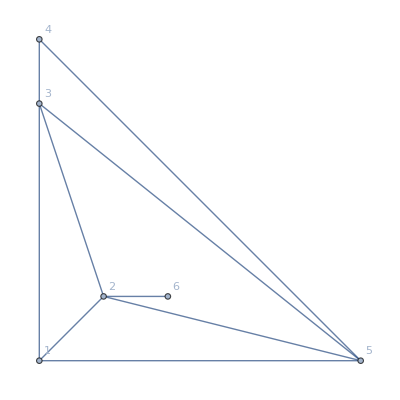

```mathematica
g2=EdgeDelete[Graph[ReadGrof[3],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"],{3<->6,4<->6,5<->6}]
```

```mathematica
ChromaticPolynomial[g1,4]
```

24

```mathematica
ChromaticPolynomial[g2,4]
```

144

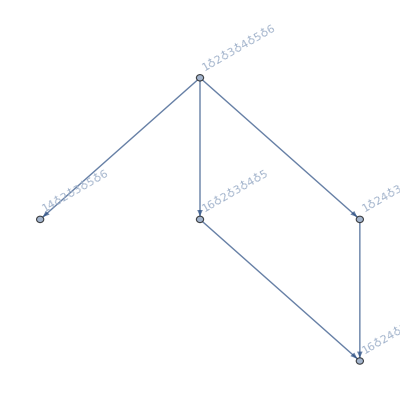

```mathematica
FindFullFormula[g1]//FormulaGraphReverse2
```

```mathematica
FindBuddyEdges[g_,e_]:=Block[{result, edges},
edges=Map[Sort,Select[EdgeList[g],#[[1]]==e[[2]]||#[[2]]==e[[2]]&]];
Print[edges,"    ", e];
result=Select[edges,(EdgeQ[g,UndirectedEdge[#[[1]],e[2]]]&&EdgeQ[g,UndirectedEdge[#[[2]],e[[1]]]])||(EdgeQ[g,UndirectedEdge[#[[2]],e[2]]]&&EdgeQ[g,UndirectedEdge[#[[1]],e[[1]]]])&];
result
]
```

```mathematica
FindBuddyEdges[ReadGrof[8],2<->3]
```

{1<->3,2<->3,3<->4,3<->5,3<->6,3<->7}    2<->3

{}

```mathematica
Graph[FormulaGraphReverse2[FindFullFormula[g2]],GraphHighlight->EdgeList[FormulaGraphReverse2[FindFullFormula[g1]]],GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
Table[With[{g=ReadGrof[k]},With[{lab=FindMPGContractionEdges[g]}, 
With[{gg=FormulaGraphReverse2[FindFullFormula[g]]},Labeled[Graph[g,VertexLabels->"Name", GraphHighlight->Map[First,lab],EdgeLabels->lab, GraphLayout->"PlanarEmbedding", GraphHighlightStyle->"Thick"]->
Table[
Labeled[Graph[FormulaGraphReverse2[FindFullFormula[EdgeDelete[g,e]]],GraphHighlight->EdgeList[gg],GraphHighlightStyle->"Thick",ImageSize->800,EdgeStyle->Map[#->Directive[DotDashed,Darker[Green],Thick]&,EdgeList[FormulaGraphReverse2[FindFullFormula[EdgeDelete[g,e]]]]]],e],{e,SetDifference[EdgeList[g],Map[First,lab]]}],ChromaticPolynomial[g,4]/24]]]
],{k,8,9}]
```

{-Graphics-→{-Graphics-2<->3,-Graphics-2<->5,-Graphics-3<->5,-Graphics-3<->6,-Graphics-3<->7,-Graphics-5<->6,-Graphics-5<->7}1,-Graphics-→{-Graphics-2<->3,-Graphics-2<->5,-Graphics-2<->6,-Graphics-3<->5,-Graphics-3<->6,-Graphics-5<->6}1}

```mathematica
Table[With[{g=ReadGrof[k]},With[{lab=FindMPGContractionEdges[g]}, 
With[{gg=FormulaGraphReverse2[FindFullFormula[g]]},Labeled[Graph[g,VertexLabels->"Name", GraphHighlight->Map[First,lab],EdgeLabels->lab, GraphLayout->"PlanarEmbedding", GraphHighlightStyle->"Thick"]->
Table[
Labeled[Graph[FormulaGraphReverse2[FindFullFormula[EdgeDelete[g,e]]],GraphHighlight->EdgeList[gg],GraphHighlightStyle->"Thick",ImageSize->800,EdgeStyle->Map[#->Directive[DotDashed,Darker[Green],Thick]&,EdgeList[FormulaGraphReverse2[FindFullFormula[EdgeDelete[g,e]]]]]],e],{e,Map[First,lab]}],ChromaticPolynomial[g,4]/24]]]
],{k,8,9}]
```

{-Graphics-→{-Graphics-1<->2,-Graphics-1<->3,-Graphics-1<->5,-Graphics-2<->7,-Graphics-3<->4,-Graphics-4<->5,-Graphics-4<->6,-Graphics-6<->7}1,-Graphics-→{-Graphics-1<->2,-Graphics-1<->3,-Graphics-1<->5,-Graphics-2<->7,-Graphics-3<->4,-Graphics-3<->7,-Graphics-4<->5,-Graphics-4<->6,-Graphics-6<->7}1}

```mathematica
Table[With[{g=MinimalGraph[k]},With[{lab=FindMPGContractionEdges[g]}, 
With[{gg=FormulaGraphReverse2[FindFullFormula[g]]},Labeled[Graph[g,VertexLabels->"Name", GraphHighlight->Map[First,lab],EdgeLabels->lab, GraphLayout->"PlanarEmbedding", GraphHighlightStyle->"Thick"]->
Table[
Labeled[Graph[FormulaGraphReverse2[FindFullFormula[EdgeDelete[g,e]]],GraphHighlight->EdgeList[gg],GraphHighlightStyle->"Thick",ImageSize->800,EdgeStyle->Map[#->Directive[DotDashed,Darker[Green],Thick]&,EdgeList[FormulaGraphReverse2[FindFullFormula[EdgeDelete[g,e]]]]]],e],{e,Map[First,lab]}],ChromaticPolynomial[g,4]/24]]]
],{k,6,6}]
```

{-Graphics-→{-Graphics-1<->3,-Graphics-3<->2,-Graphics-3<->4,-Graphics-4<->5,-Graphics-5<->6,-Graphics-1<->7,-Graphics-2<->7,-Graphics-6<->7}1}